```mathematica
f[n_] := Simplify[Integrate[r^n Exp[-r^2 SNR], {r, μ, ∞}], Assumptions -> {Re[SNR] > 0∧ μ > 0 ∧ n >= 0}]
```

```mathematica
f0=f[0];
```

```mathematica
f1=f[1];
```

```mathematica
f2 = f[2];
```

```mathematica
f3=f[3];
```

```mathematica
f4=f[4];
```

```mathematica
f5 = f[5];
```

```mathematica
f6 = f[6];
```

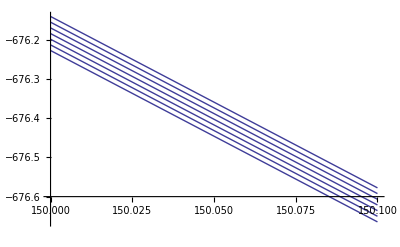

```mathematica
Plot[10 Log[10,{f0, f1, f2, f3,f4, f5,f6}] /. μ -> 1, {SNR, 150, 150.1}]
```